## Compare to Alice Data

{{1,PT [GEV]},{2,PT [GEV] LOW},{3,PT [GEV] HIGH},{4,(1/Nev)*(1/(2*PI*PT))*D2(N)/DPT/DYRAP [GEV**-2]},{5,stat +},{6,stat -},{7,sys +},{8,sys -},{9,sys,normalization uncertainty +},{10,sys,normalization uncertainty -}}

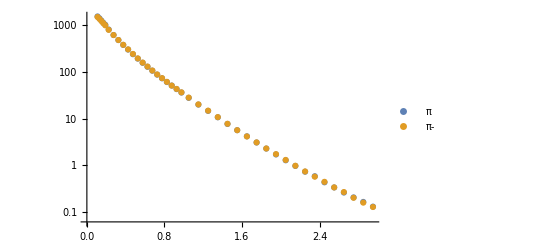

```mathematica
ALICEdatatxt=Import[StringJoin[NotebookDirectory[],"data/HEPData-ins1222333-v1-Table_1.csv"],"Text"];
(*ALICEdata=ImportString[StringReplace[StringReplace[ALICEdatatxt,RegularExpression["\n+"]->"\n"],StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"CSV"];*)
ALICEdata=ImportString[StringReplace[Alicedatatxt,StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"CSV","IgnoreEmptyLines"->True];
MatrixForm[ALICEdata];
titles=ALICEdata[[1]];
enumeratedtitles=Transpose[{Range[Length[titles]],titles}]
πplus=ALICEdata[[2;;42]];
πminus=Alicedata[[44;;]];
ALICEps=(Transpose@πplus)[[1]];
ALICEpiplus=(Transpose@πplus)[[4]];
ALICEpiminus=(Transpose@πminus)[[4]];

ListLogPlot[{Transpose@{ALICEps,ALICEpiplus},Transpose@{ALICEps,ALICEpiminus}},PlotLegends->{"π","π-"}]
```

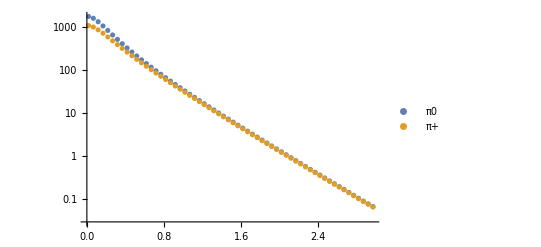

```mathematica
Fluidumdata=Import[StringJoin[NotebookDirectory[],"data/pionListBig.txt"],"CSV"];
Fluidumps=Fluidumdata[[1]];
Fluidumpi0=Fluidumdata[[2]];
Fluidumpiplus=Fluidumdata[[3]];

ListLogPlot[{Transpose@{Fluidumps,Fluidumpi0},Transpose@{Fluidumps,Fluidumpiplus}},PlotLegends->{"π0","π+"}]
```

SetDelayed::write: Tag InterpolatingFunction in InterpolatingFunction[{{0.11,2.95}},{5,7,0,{41},{4},0,0,0,0,Automatic,«3»},{{0.11,0.13,0.15,0.17,0.19,0.225,0.275,0.325,0.375,0.425,«31»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«32»},{1543.,1404.,1258.,1125.,1022.,809.9,618.3,481.9,379.4,301.4,«31»}},{Automatic}][p_] is Protected.

SetDelayed::write: Tag InterpolatingFunction in InterpolatingFunction[{{0.017,2.967}},{5,7,0,{60},{4},0,0,0,0,Automatic,«3»},{{0.017,0.067,0.117,0.167,0.217,0.267,0.317,0.367,0.417,0.467,«50»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«51»},{1090.81,1007.61,869.516,723.609,592.62,482.875,393.463,321.427,263.525,216.894,«50»}},{Automatic}][p_] is Protected.

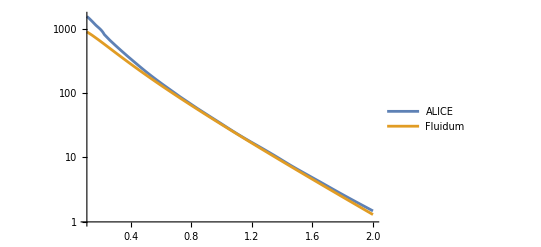

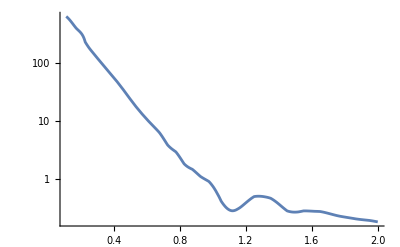

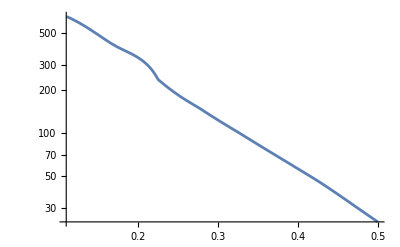

```mathematica
ALICEcurvelog=Interpolation[Transpose@{ALICEps,Log@ALICEpiplus}];
Fluidumcurvelog=Interpolation[Transpose@{Fluidumps,Log@Fluidumpiplus}];

ALICEcurve[p_]:=Exp@ALICEcurvelog[p];
Fluidumcurve[p_]:=Exp@Fluidumcurvelog[p];

pmin=Max[Min[ALICEps],Min[Fluidumps]];

LogPlot[{ALICEcurve[p],Fluidumcurve[p]},{p,pmin,2},PlotLegends->{"ALICE","Fluidum"}]
LogPlot[ALICEcurve[p]-Fluidumcurve[p],{p,pmin,2}]
LogPlot[ALICEcurve[p]-Fluidumcurve[p],{p,pmin,0.5}]
```

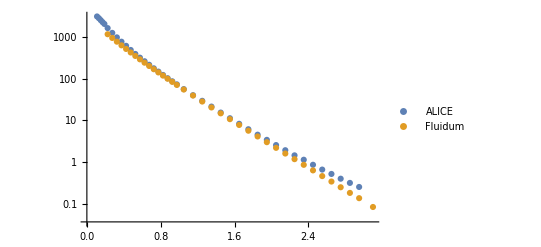

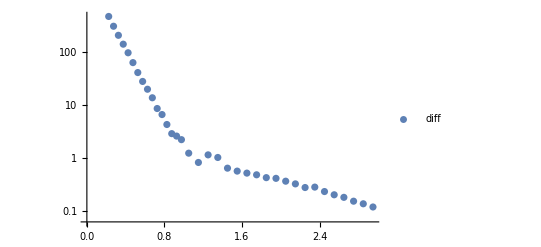

```mathematica
ListALICE=Transpose@{aliceps,aliceyieldplus+aliceyieldminus};
ListFluidum=Transpose@{Fluidumdata[[1]],2*Fluidumdata[[2]]};
ListLogPlot[
{ListALICE,
ListFluidum},
PlotLegends->{"ALICE","Fluidum"}
]

diff=(Transpose@ListALICE)[[2]][[6;;]]-(Transpose@ListFluidum)[[2]][[;;-2]];
Listdiff=Transpose@{(Transpose@ListALICE)[[1]][[6;;]],diff};
ListLogPlot[Listdiff,PlotLegends->{"diff"}]
```

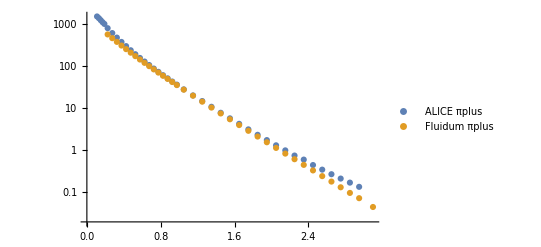

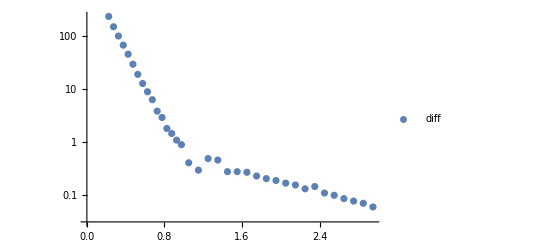

```mathematica
ListALICEπplus=Transpose@{aliceps,aliceyieldplus};
ListFluidumπplus=Transpose@{Fluidumdata[[1]],Fluidumdata[[2]]};
ListLogPlot[
{ListALICEπplus,
ListFluidumπplus},
PlotLegends->{"ALICE πplus","Fluidum πplus"}
]

diff=(Transpose@ListALICEπplus)[[2]][[6;;]]-(Transpose@ListFluidumπplus)[[2]][[;;-2]];
Listdiff=Transpose@{(Transpose@ListALICEπplus)[[1]][[6;;]],diff};
ListLogPlot[Listdiff,PlotLegends->{"diff"}]
```

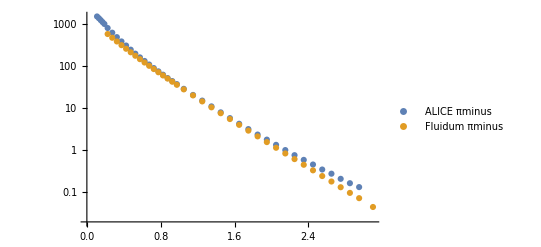

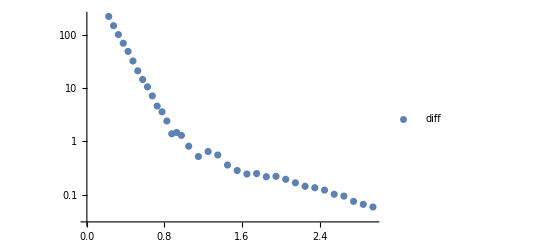

```mathematica
ListALICEπminus=Transpose@{aliceps,aliceyieldminus};
ListFluidumπminus=Transpose@{Fluidumdata[[1]],Fluidumdata[[2]]};
ListLogPlot[
{ListALICEπminus,
ListFluidumπminus},
PlotLegends->{"ALICE πminus","Fluidum πminus"}
]

diff=(Transpose@ListALICEπminus)[[2]][[6;;]]-(Transpose@ListFluidumπminus)[[2]][[;;-2]];
Listdiff=Transpose@{(Transpose@ListALICEπminus)[[1]][[6;;]],diff};
ListLogPlot[Listdiff,PlotLegends->{"diff"}]
```